```mathematica
ClearAll["Global`*"]
```

```mathematica
rhorcb=Matm  (Rbp/Rrcb)^(1/(-gamma+1)) / (4 A Pi Rrcb^3)
```

(Matm (Rbp/Rrcb)^(1/(1-gamma)))/(4 A π Rrcb^3)

```mathematica
En=-(gamma-1)^2/(A gamma (3-2 gamma)) G Mc Matm / Rc (Rrcb/Rc)^(-(3 gamma-4)/(gamma-1))
```

-(G (-1+gamma)^2 Matm Mc (Rrcb/Rc)^((4-3 gamma)/(-1+gamma)))/(A (3-2 gamma) gamma Rc)

```mathematica
L= 64 Pi/3 sigma Trcb^4 Rbp/(kappa rhorcb)
```

(256 A π^2 Rbp (Rbp/Rrcb)^(-1/(1-gamma)) Rrcb^3 sigma Trcb^4)/(3 kappa Matm)

```mathematica
Trcb=(gamma-1)/gamma G Mc mu/(Rbp kb)
```

(G (-1+gamma) Mc mu)/(gamma kb Rbp)

```mathematica
time=-En/L
```

(3 gamma^3 kappa kb^4 Matm^2 Rbp^3 (Rbp/Rrcb)^(1/(1-gamma)) (Rrcb/Rc)^((4-3 gamma)/(-1+gamma)))/(256 A^2 G^3 (3-2 gamma) (-1+gamma)^2 Mc^3 mu^4 π^2 Rc Rrcb^3 sigma)

```mathematica
Rrcb=Rbp;
```

```mathematica
sol=Solve[time==t, Matm];
```

```mathematica
Matm=Matm/.sol[[2]]
```

(16 A G^(3/2) √(3-2 gamma) (-1+gamma) Mc^(3/2) mu^2 π (Rbp/Rc)^(-(4-3 gamma)/(2 (-1+gamma))) √Rc √sigma √t)/(√3 gamma^(3/2) √kappa kb^2)

```mathematica
L
```

(16 G^(5/2) (-1+gamma)^3 Mc^(5/2) mu^2 π (Rbp/Rc)^((4-3 gamma)/(2 (-1+gamma))) √sigma)/(√3 √(3-2 gamma) gamma^(5/2) √kappa kb^2 √Rc √t)

```mathematica
mp=1.67*^-24;
G=6.67*^-8;
sigma=5.67*^-5;
Me=6*^27;
kb=1.38*^-16;
yr=365*24*3600;
```

```mathematica
mu=2.35 mp;
Td=1000;
rhoc=2;
kappa=0.1;
gamma=7/5;
Mc=10 Me;
Rbp= G Mc mu/(kb Td) (gamma-1)/gamma;
Rc=(3 Mc/(4 Pi rhoc))^(1/3);
cs=Sqrt[kb Td/(mu)];
gammac=4/3;
muc=60 mp;
```

```mathematica
A=5 Pi/16;
```

```mathematica
L=(16 G^(5/2) (-1+gamma)^3 Mc^(5/2) mu^2 π (Rbp/Rc)^((4-3 gamma)/(2 (-1+gamma))) √sigma)/(√3 √(3-2 gamma) gamma^(5/2) √kappa kb^2 √Rc √tcool)
```

(3.92706×10^32)/(√tcool)

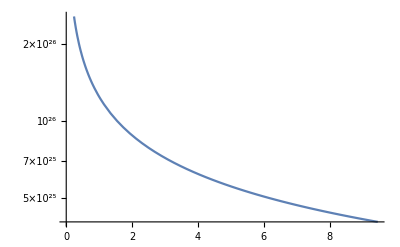

```mathematica
LogPlot[L, {tcool, 1 yr, 3*^6 yr }]
```

```mathematica
t=3 10^6 yr;
```

```mathematica
td=3 10^6 yr;
```

```mathematica
tevapf=td*(Rbp/Rc)^(-(3-2 gamma)/(gamma-1)) A gamma (3-2 gamma) / (gamma-1)^2
```

3.95744×10^13

```mathematica
Rbp
```

3.25173×10^10

```mathematica
rhorcb
```

0.0000306057

```mathematica
Rbp/Rc
```

16.8695

```mathematica
Rrcbevap=Rc;
```

```mathematica
rhorcbevap=0.00003060569962797434;
```

```mathematica
Matmevap=A 4 Pi Rrcbevap^3 rhorcbevap (Rbp/Rrcbevap)^(1/(gamma-1))
```

3.16085×10^27

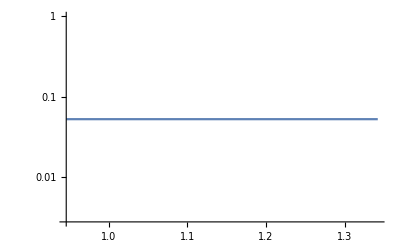

```mathematica
LogPlot[Matmevap/Mc, {tevap, td, td+tevapf}]
```

```mathematica
Levap= 64 Pi/3 sigma Trcb^4 Rbp/(kappa rhorcbevap)
```

4.03742×10^25

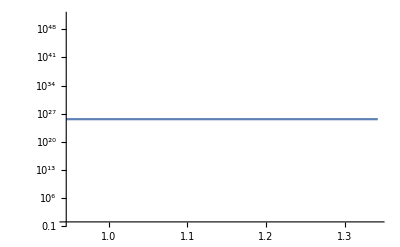

```mathematica
LogPlot[Levap, {tevap, td, td+tevapf}]
```

```mathematica
t=3*^6 yr;
```

```mathematica
L
```

(3.92706×10^32)/(√tcool)

```mathematica
Matm/Mc
```

0.216373

```mathematica
Clear[tshrink, Rrcbshrink]
```

```mathematica
sol2=Solve[tshrink == 1/(256 Pi^2) 3gamma^2/(gamma-1)^2 kb/mu Matmevap/(sigma Td^3 Rc^4) (Rbp Rrcbshrink/Rc^2)^(-1/(gamma-1)) * (gamma/(2 gamma-1) Matmevap+1/gamma (gamma-1)/(gammac-1) mu/muc Mc), Rrcbshrink]
```

{{Rrcbshrink→(4.40689×10^15)/tshrink^(2/5)}}

```mathematica
Rrcbshrink=Rrcbshrink/.sol2[[1]]
```

(4.40689×10^15)/tshrink^(2/5)

```mathematica
rhorcbshrink=Matmevap gamma/(gamma-1)1/(4 Pi Rc^2 Rrcbshrink) (Rc^2/(Rbp Rrcbshrink))^(1/(gamma-1))
```

5.82032×10^-27 tshrink^(7/5)

```mathematica
Lshrink=64 Pi/3 sigma Trcb^4 Rbp/(kappa rhorcbshrink)
```

(2.12304×10^47)/tshrink^(7/5)

```mathematica
thsrinkf=1/(256 Pi^2) 3gamma^2/(gamma-1) kb/mu Matm /(sigma Td^3 Rc^4) (Rbp Rrcbevap/Rc^2)^(-1/(gamma-1)) * (gamma/(2 gamma-1) Matm+1/gamma (gamma-1)/(gammac-1) mu/muc Mc)
```

2.74184×10^15

```mathematica
4.4831*10^34/thsrinkf^(2/5)
```

2.99476×10^28

```mathematica
(Rc/Rbp)^(1./2)
```

0.130141

```mathematica
N[Rc]
```

1.92757×10^9

```mathematica
LogPlot[Lshrink, {tshrink, td+tevapf, 10^9 yr}]
```

-Graphics-

```mathematica
tthinf=Rbp/cs (Rc/Rbp)^((3 gamma-4)/(gamma-1)) Exp[Rbp gamma/(gamma-1)/Rc/2 -1]
```

1.02881×10^17

```mathematica
td+tevapf
```

1.17642×10^14

```mathematica
tthinf/yr
```

3.26233×10^9

```mathematica
Clear[tthin, Matmthin]
```

```mathematica
sol3=Solve[tthin == 1/(256 Pi^2) 3gamma^2/(gamma-1) kb/mu Matmthin/(sigma Td^3 Rc^4) (Rbp Rrcbevap/Rc^2)^(-1/(gamma-1)) * (gamma/(2 gamma-1) Matmthin+1/gamma (gamma-1)/(gammac-1) mu/muc Mc), Matmthin]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Matmthin→0.428571 (-3.02143×10^27-3.74166 √(6.52074×10^53+2.23606×10^39 tthin))},{Matmthin→0.428571 (-3.02143×10^27+3.74166 √(6.52074×10^53+2.23606×10^39 tthin))}}

```mathematica
Matmthin=Matmthin/.sol3[[2]]
```

0.428571 (-3.02143×10^27+3.74166 √(6.52074×10^53+2.23606×10^39 tthin))

```mathematica
tthin=1.06 10^14
```

1.06×10^14

```mathematica
Matmthin/Mc
```

0.00361893

```mathematica
rhorcbthin=Matmthin gamma / (gamma-1) 1/(4 Pi Rc^2 Rrcbevap) (Rc^2/(Rbp Rrcbevap))^(1/(gamma-1))
```

1.4259×10^-32 (-3.02143×10^27+3.74166 √(6.52074×10^53+2.23606×10^39 tthin))

```mathematica
Lthin= 64 Pi/3 sigma Trcb^4 Rbp/(kappa rhorcbthin)
```

(8.66594×10^52)/(-3.02143×10^27+3.74166 √(6.52074×10^53+2.23606×10^39 tthin))

```mathematica
LogPlot[Lthin, {tthin, 1.06 10^14, 10^9 yr}]
```

-Graphics-

```mathematica
Luminosity[t_]:=Piecewise[{{3.92706 10^32/Sqrt[t yr], t yr≤ td}, {Levap, td<t yr<td+tevapf}, {3.2 10^45/(t yr)^(7/5), t yr≥ tevapf + td}}]
```

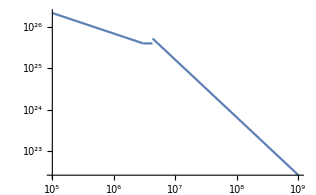

```mathematica
LogLogPlot[Luminosity[t], {t, 10^5  , 10^9 }]
```

```mathematica
tevapf/yr
```

1.2549×10^6

```mathematica
L
```

(3.92706×10^32)/(√tcool)

```mathematica
Levap
```

4.03742×10^25

```mathematica
Lshrink
```

(3.2027×10^45)/tshrink^(7/5)